## VO2 temperature transformation

#### Import data

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b"]
vo2Data=ReadList["allBands.out",Table[Number,{i,1,23}]][[1;;707]];
Tc=340.65;
T0=329.65;
Tfrac=(Tc-T0)/Tc;
omega0R=-10.7507508144;
```

/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b

```mathematica
vo2Data[[-1]]
```

{707,0.,0.,0.,-0.00563432,-0.004994,-0.004994,4.46923,5.57429,5.84174,6.65076,6.65076,11.6386,11.6386,12.4359,12.4359,12.6051,13.0563,14.1324,17.5391,18.7565,0.0333687,0}

```mathematica
qList;
```

```mathematica
vo2Data[[-2]]
```

{707,0.,0.,0.,-0.00563432,-0.004994,-0.004994,4.46923,5.57429,5.84174,6.65076,6.65076,11.6386,11.6386,12.4359,12.4359,12.6051,13.0563,14.1324,17.5391,18.7565,0.0333687,0}

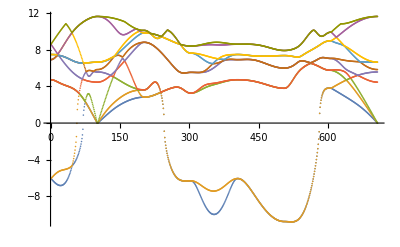

```mathematica
originalBandi[i_]:=Transpose@{Transpose[vo2Data][[1]],Transpose[vo2Data][[4+i]]}
ListPlot@Table[originalBandi[i],{i,1,10}]
```

#### Transformation functions

```mathematica
(*Define linear or FD shift function*)
tFunction[arg_,beta_,mu_]:=1/(Exp[-beta*(arg/0.5-mu)]+1)
tFunctionLin[arg_,beta_,mu_]:=arg/0.5
tFunctionPiece[arg_]:=If[arg==0,1,If[arg/0.5==1,1,0]]
```

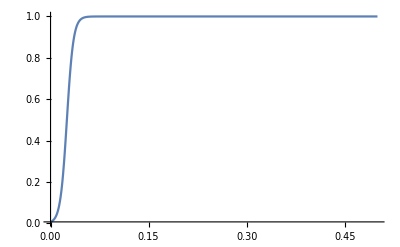

```mathematica
Plot[tFunction[arg,100,0.05],{arg,0,0.5},PlotRange->All]
```

#### Select the transition bands by hand

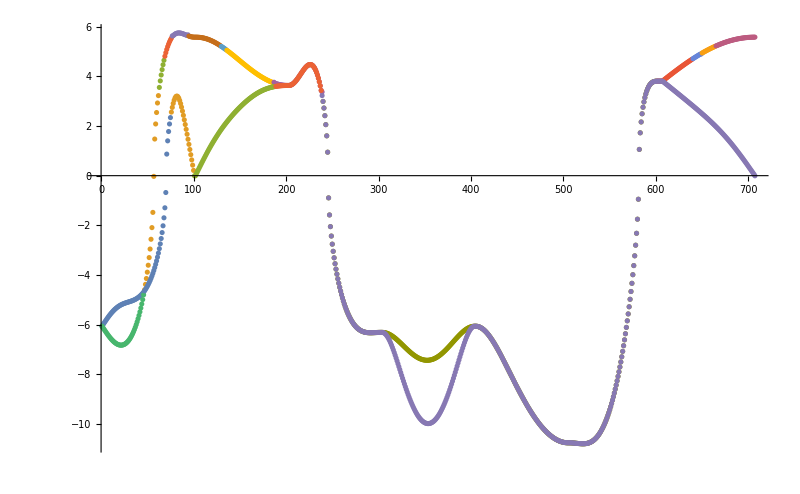

```mathematica
l1={originalBandi[1][[1;;46]],originalBandi[1][[47;;75]],originalBandi[3][[76;;100]],originalBandi[2][[101;;188]],originalBandi[3][[189;;238]],originalBandi[1][[239;;707]]};
l2={originalBandi[2][[1;;46]],originalBandi[2][[47;;62]],originalBandi[4][[63;;68]],originalBandi[5][[69;;76]],originalBandi[6][[77;;94]],originalBandi[5][[95;;129]],originalBandi[4][[130;;135]],originalBandi[3][[136;;186]],originalBandi[4][[187;;239]],originalBandi[2][[240;;600]],originalBandi[2][[601;;639]],originalBandi[3][[640;;649]],originalBandi[4][[650;;664]],originalBandi[5][[665;;707]]};
ListPlot[(Join@@{l2,l1}),ImageSize->800,PlotRange->All]
```

```mathematica
band1EnergiesPreTransform=Transpose[Join@@l1][[2]];
band2EnergiesPreTransform=Transpose[Join@@l2][[2]];
qBand1EnergiesPreTransform=Table[Join[qList[[i]],{band1EnergiesPreTransform[[i]]}],{i,1,707}];
qBand2EnergiesPreTransform=Table[Join[qList[[i]],{band2EnergiesPreTransform[[i]]}],{i,1,707}];
band1MapData={qList[[1;;707]]->band1EnergiesPreTransform};
band2MapData={qList[[1;;707]]->band2EnergiesPreTransform};
```

```mathematica
band1MapDataExtra=Join[qList[[1;;707]],{#[[1]],#[[2]],#[[3]]}&/@qGE3denseList1b1]->Join[band1EnergiesPreTransform,#[[4]]&/@qGE3denseList1b1];
band2MapDataExtra=Join[qList[[1;;707]],{#[[1]],#[[2]],#[[3]]}&/@qGE3denseList2b2]->Join[band2EnergiesPreTransform,#[[4]]&/@qGE3denseList2b2];
```

```mathematica
band2MapDataExtra;
```

```mathematica
band1GP=Predict[band1MapData[[1]],Method->"GaussianProcess",PerformanceGoal->"Quality"]
band2GP=Predict[band2MapData[[1]],Method->"GaussianProcess",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

PredictorFunction[…]

```mathematica
band1GPextra=Predict[band1MapDataExtra,Method->"GaussianProcess",PerformanceGoal->"Quality"]
band2GPextra=Predict[band2MapDataExtra,Method->"GaussianProcess",PerformanceGoal->"Quality"]
```

PredictorFunction[…]

PredictorFunction[…]

```mathematica
gp1List=Table[band1GP[qList[[i]]],{i,1,707}];
gp2List=Table[band2GP[qList[[i]]],{i,1,707}];
```

```mathematica
gp1Listextra=Table[band1GPextra[qList[[i]]],{i,1,707}];
gp2Listextra=Table[band2GPextra[qList[[i]]],{i,1,707}];
```

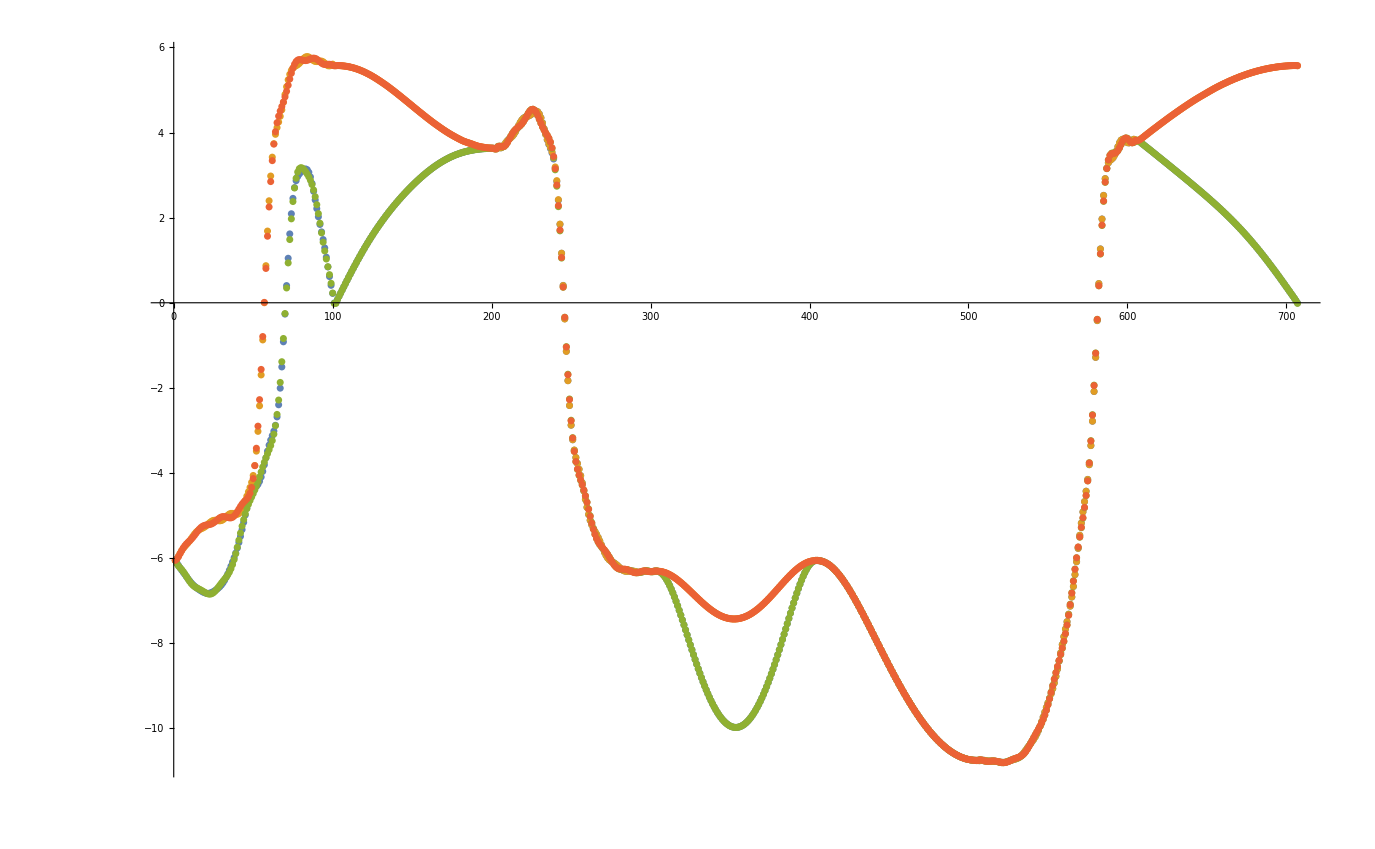

```mathematica
ListPlot[{gp1List,gp2List,gp1Listextra,gp2Listextra}]
```

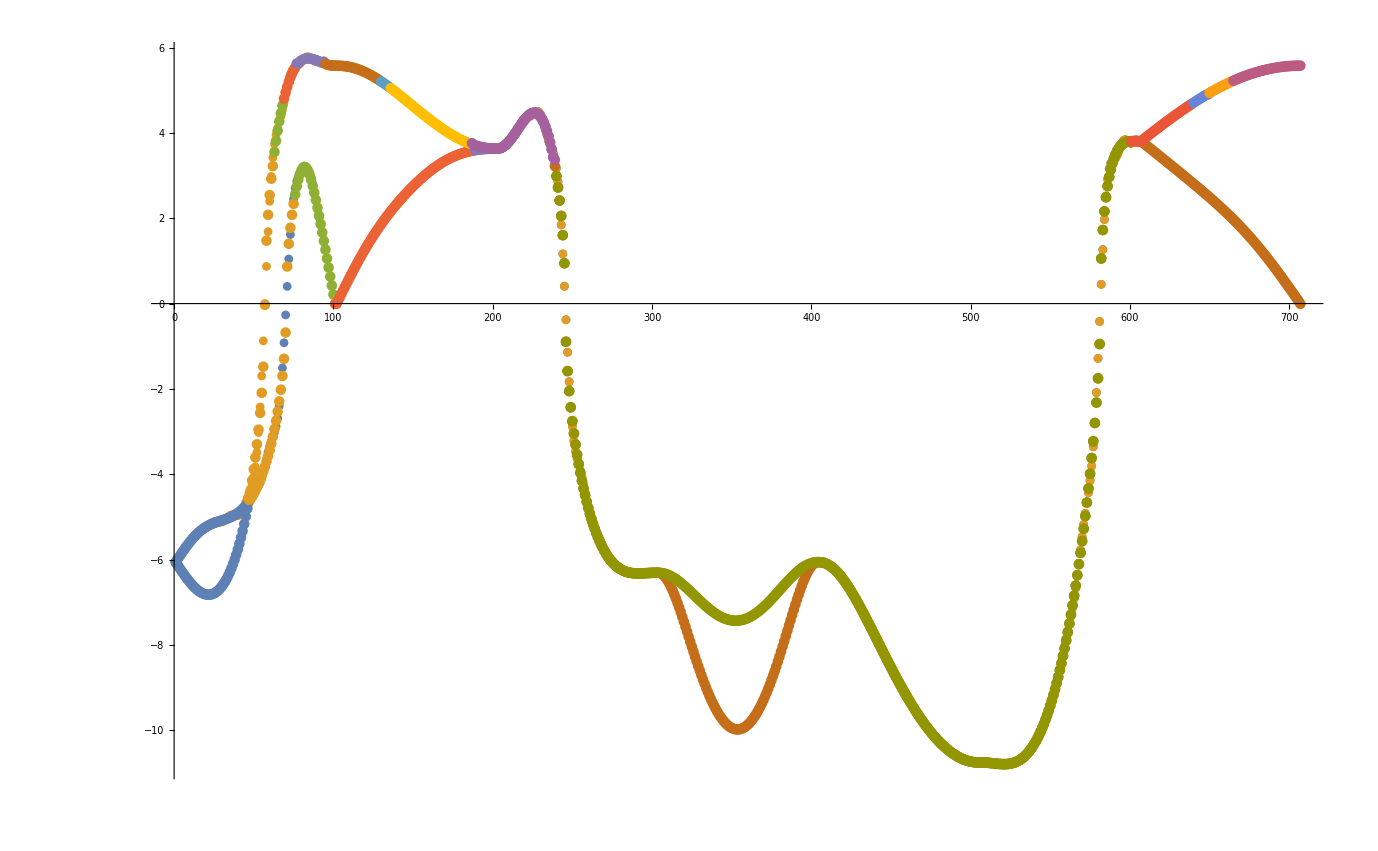

```mathematica
Show[ListPlot[{gp1List,gp2List}],ListPlot[Join@@{l1}],ListPlot[Join@@{l2}]]
```

```mathematica
b1twoD=Join@@Table[{y,z,band1GP[{0,y,z}]},{y,0,0.5,0.01},{z,0,0.5,0.01}]
```

{{0.,0.,-0.00411585},{0.,0.01,0.409825},{0.,0.02,0.842038},{0.,0.03,1.28894},{0.,0.04,1.66545},{0.,0.05,2.01991},{0.,0.06,2.41591},{0.,0.07,2.80454},{0.,0.08,3.0655},2583,{0.5,0.42,-10.7991},{0.5,0.43,-10.7914},{0.5,0.44,-10.7782},{0.5,0.45,-10.7742},{0.5,0.46,-10.7757},{0.5,0.47,-10.7671},{0.5,0.48,-10.751},{0.5,0.49,-10.7525},{0.5,0.5,-10.7493}}
 |  |  |  |

```mathematica
b1twoD=Join@@Table[{y,z,band1GP[{0,y,z}]},{y,0,0.5,0.01},{z,0,0.5,0.01}]
```

{{0.,0.,-0.00411585},{0.,0.01,0.409825},{0.,0.02,0.842038},{0.,0.03,1.28894},{0.,0.04,1.66545},{0.,0.05,2.01991},2589,{0.5,0.45,-10.7742},{0.5,0.46,-10.7757},{0.5,0.47,-10.7671},{0.5,0.48,-10.751},{0.5,0.49,-10.7525},{0.5,0.5,-10.7493}}
 |  |  |  |

```mathematica
b1twoDxtra=Join@@Table[{y,z,band1GPextra[{0,y,z}]},{y,0,0.5,0.01},{z,0,0.5,0.01}]
```

{{0.,0.,-0.0142333},{0.,0.01,0.457708},{0.,0.02,0.846455},{0.,0.03,1.21749},{0.,0.04,1.64169},{0.,0.05,2.09413},2589,{0.5,0.45,-10.7636},{0.5,0.46,-10.7643},{0.5,0.47,-10.7734},{0.5,0.48,-10.7669},{0.5,0.49,-10.74},{0.5,0.5,-10.7567}}
 |  |  |  |

```mathematica
ListPointPlot3D@b1twoD
ListPointPlot3D@b1twoDxtra
```

-Graphics3D-

-Graphics3D-

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b/"]
list=ReadList["mesh.out",Table[Number,{i,21}]];
qListSmall={#[[1]],#[[2]],#[[3]]}&/@list;
eListSmall=Table[#[[3+i]],{i,1,18}]&/@list;
fx[band_]:={#[[2]],#[[3]],#[[band+3]]}&/@list;
```

/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b

```mathematica
data2p=Join@@Table[{y,z,band2GPextra[{0,y,z}]},{y,0,0.5,0.1},{z,0,0.5,0.1}]
data1p=Join@@Table[{y,z,band1GPextra[{0,y,z}]},{y,0,0.5,0.1},{z,0,0.5,0.1}]
```

{{0.,0.,5.57034},{0.,0.1,5.70057},{0.,0.2,2.847},{0.,0.3,-4.84672},{0.,0.4,-5.21852},{0.,0.5,-6.05198},{0.1,0.,5.49329},{0.1,0.1,2.19211},{0.1,0.2,-0.840705},{0.1,0.3,-4.05564},{0.1,0.4,-5.16504},{0.1,0.5,-6.73929},{0.2,0.,5.25401},{0.2,0.1,0.431719},{0.2,0.2,-2.5492},{0.2,0.3,-3.25325},{0.2,0.4,-5.19262},{0.2,0.5,-8.15741},{0.3,0.,4.86887},{0.3,0.1,0.256512},{0.3,0.2,-2.62319},{0.3,0.3,-3.02044},{0.3,0.4,-5.47306},{0.3,0.5,-9.51408},{0.4,0.,4.37425},{0.4,0.1,1.0337},{0.4,0.2,-3.89339},{0.4,0.3,-5.22767},{0.4,0.4,-7.36456},{0.4,0.5,-10.4305},{0.5,0.,3.8141},{0.5,0.1,2.83686},{0.5,0.2,-6.5417},{0.5,0.3,-9.87119},{0.5,0.4,-10.7624},{0.5,0.5,-10.756}}

{{0.,0.,-0.0142333},{0.,0.1,3.16234},{0.,0.2,-3.3552},{0.,0.3,-5.57831},{0.,0.4,-6.83257},{0.,0.5,-6.05249},{0.1,0.,1.03175},{0.1,0.1,-0.0729792},{0.1,0.2,-3.75563},{0.1,0.3,-5.12551},{0.1,0.4,-6.31198},{0.1,0.5,-6.73928},{0.2,0.,1.89368},{0.2,0.1,-1.56668},{0.2,0.2,-3.91814},{0.2,0.3,-4.57239},{0.2,0.4,-6.11345},{0.2,0.5,-8.15742},{0.3,0.,2.5858},{0.3,0.1,-1.31385},{0.3,0.2,-3.88832},{0.3,0.3,-4.28712},{0.3,0.4,-6.32499},{0.3,0.5,-9.51407},{0.4,0.,3.20514},{0.4,0.1,0.155894},{0.4,0.2,-4.76268},{0.4,0.3,-6.13585},{0.4,0.4,-7.97639},{0.4,0.5,-10.4305},{0.5,0.,3.81978},{0.5,0.1,2.82878},{0.5,0.2,-6.53296},{0.5,0.3,-9.878},{0.5,0.4,-10.7569},{0.5,0.5,-10.7567}}

```mathematica
ListPlot3D[{data1p,data2p}]
```

-Graphics3D-

```mathematica
band1GP[{0.4375,0.3125,0.4375}]
band2GP[{0.4375,0.3125,0.4375}]
band1GPextra[{0.4375,0.3125,0.4375}]
band2GPextra[{0.4375,0.3125,0.4375}]
```

-4.04534

-2.73384

-8.76907

-7.78331

```mathematica
band1GP[{0.4375,0.4375,0.4375}]
band2GP[{0.4375,0.4375,0.4375}]
```

-5.77973

-5.06497

```mathematica
list[[39;;40]]
```

{{0.4375,0.3125,0.4375,-8.67632,-7.6184,4.09269,4.18331,5.58951,5.66725,7.20833,7.60894,8.56411,8.65275,10.8373,11.0796,13.556,13.7335,15.2381,15.7158,18.285,18.4109},{0.4375,0.4375,0.4375,-7.09769,-6.50285,3.70538,3.70628,5.47448,5.49831,7.75656,7.9346,8.49396,8.52416,10.6707,10.8337,13.7839,13.8779,15.2417,15.4113,18.6177,18.6559}}

```mathematica
eListSmall[[1]]
```

{1.2847,1.81938,2.92638,4.676,5.50385,5.69044,6.69159,6.71074,11.3827,11.4858,12.2445,12.5314,12.552,12.9132,14.5028,17.3169,17.4325,18.8348}

```mathematica
eListSmall//Length
```

40

```mathematica
qListSmallGP1=Table[Join@@{qListSmall[[i]],{band1GPextra[qListSmall[[i]]]}},{i,1,Length@qListSmall}];
qListSmallGPE1=Table[band1GPextra[qListSmall[[i]]],{i,1,Length@qListSmall}];
qListSmallGP2=Table[Join@@{qListSmall[[i]],{band2GPextra[qListSmall[[i]]]}},{i,1,Length@qListSmall}];
qListSmallGPE2=Table[band2GPextra[qListSmall[[i]]],{i,1,Length@qListSmall}];
```

```mathematica
band1GPextra[{0.0625,0.0625,0.0625}]
```

1.14895

```mathematica
qListSmallGP1[[2]]
eListSmall[[2]]
```

{0.1875,0.0625,0.0625,-2.35227}

{2.07462,2.69948,4.21313,5.17524,5.45584,6.32999,6.75064,7.25653,10.9398,11.2953,11.8708,12.5446,12.5741,12.7243,14.7745,16.9875,17.5703,19.0024}

```mathematica
qListSmallGP2[[36]]
eListSmall[[36]]
```

{0.3125,0.1875,0.4375,-8.1518}

{-10.1691,-8.05725,4.1924,4.73363,6.08705,6.41638,6.71942,7.41374,8.42546,8.93681,11.2873,11.446,13.0208,13.3655,15.0704,16.5583,17.5425,18.1266}

```mathematica
mins1=Min/@Table[eListSmall[[i]]-qListSmallGPE1[[i]],{i,1,40}]
difs1=Table[eListSmall[[i]]-qListSmallGPE1[[i]],{i,1,40}];
mins2=Min/@Table[eListSmall[[i]]-qListSmallGPE2[[i]],{i,1,40}]
difs2=Table[eListSmall[[i]]-qListSmallGPE2[[i]],{i,1,40}];
```

{0.135754,4.4269,6.60404,7.38279,1.46318,4.50584,7.16392,1.43442,4.69558,0.297819,0.0854291,-0.38,-1.01919,-1.23568,-1.09447,-1.09458,-0.66249,-0.782163,0.350593,-0.293583,-0.138007,-0.168759,-0.157709,-0.0844668,-0.483276,-0.389054,-0.172737,-0.477972,-0.187724,-0.0912215,-0.0267124,0.125796,0.252786,0.405643,-0.0506484,0.0586072,0.230138,-0.0537739,0.0927463,-0.00736513}

{-2.88095,2.62134,5.31892,6.11563,-0.690476,3.15824,5.92441,0.416968,3.77341,0.0699401,-3.64252,-1.77609,-2.27894,-2.44409,-2.54328,-2.49317,-1.92213,-2.16686,-0.870614,-0.913224,-1.21673,-1.43833,-1.05428,-0.431818,-3.00629,-2.56858,-1.02336,-2.95449,-1.32457,-0.805975,-1.2202,-1.09437,-0.537467,0.217807,-2.48459,-2.01732,-0.476949,-2.40138,-0.893014,-0.596942}

```mathematica
qListSmallGP1=Table[Join@@{qListSmall[[i]],{band1GP[qListSmall[[i]]]}},{i,1,Length@qListSmall}];
qListSmallGPE1=Table[band1GP[qListSmall[[i]]],{i,1,Length@qListSmall}];
qListSmallGP2=Table[Join@@{qListSmall[[i]],{band2GP[qListSmall[[i]]]}},{i,1,Length@qListSmall}];
qListSmallGPE2=Table[band2GP[qListSmall[[i]]],{i,1,Length@qListSmall}];
```

```mathematica
mins1=Min/@Table[eListSmall[[i]]-qListSmallGPE1[[i]],{i,1,18}]
difs1=Table[eListSmall[[i]]-qListSmallGPE1[[i]],{i,1,18}];
mins2=Min/@Table[eListSmall[[i]]-qListSmallGPE2[[i]],{i,1,18}]
difs2=Table[eListSmall[[i]]-qListSmallGPE2[[i]],{i,1,18}];
```

{1.08203,4.57016,5.97343,6.5934,1.93614,4.93017,6.56312,2.0203,5.27386,1.2697,-0.339452,-1.49322,-2.43897,-2.75732,-2.11676,-2.35427,-2.07814,-1.76776}

{-1.93472,2.9638,4.70289,5.32749,-0.111156,3.5825,5.29769,0.907196,4.1325,0.807312,-3.12986,-2.77236,-3.70493,-4.02323,-3.39217,-3.62124,-3.34405,-3.0324}

```mathematica
difs1
```

{{0.135754,0.670434,1.77743,3.52705,4.35491,4.5415,5.54264,5.56179,10.2337,10.3369,11.0956,11.3824,11.4031,11.7642,13.3538,16.168,16.2835,17.6858},{4.4269,5.05176,6.56541,7.52751,7.80812,8.68226,9.10291,9.6088,13.2921,13.6476,14.2231,14.8968,14.9264,15.0766,17.1267,19.3398,19.9226,21.3547},{6.60404,7.69659,8.93052,9.51729,9.67902,10.7299,11.4328,11.8756,14.0388,14.7112,15.1014,15.9146,16.4587,16.5694,19.0318,20.3803,21.7546,22.8816},{7.38279,7.93365,9.7522,9.96957,10.6466,11.1625,12.5938,13.017,13.3897,14.2067,14.9084,15.4223,16.7059,16.7512,19.6619,20.1089,22.4161,22.8465},{1.46318,2.42163,4.39214,5.24788,5.37353,6.59375,6.88784,6.90005,9.90479,10.8447,11.0723,11.9739,12.2304,12.2504,14.6025,16.6671,17.0944,18.5997},{4.50584,5.30964,6.44698,8.11978,8.52327,9.11114,9.82921,10.0298,11.5884,12.6682,13.0266,13.7768,14.5382,14.5643,17.3125,18.7411,19.6559,20.8182},{7.16392,7.63134,8.86111,10.1388,10.5795,10.6942,12.6602,13.028,13.4737,13.841,14.7622,15.1049,16.499,16.5164,19.7523,20.2489,22.083,22.5135},{1.43442,2.50738,3.17992,5.51715,5.96577,6.55727,7.38961,7.68098,8.63962,9.61852,9.78614,10.4947,11.6148,11.6919,14.8744,16.2609,16.5701,17.734},{4.69558,5.23216,5.84856,6.88263,9.17965,9.44355,10.8095,11.0344,11.4548,11.6699,12.3178,12.6303,14.2806,14.3163,18.0735,18.6057,19.6201,20.0685},{0.297819,0.701583,1.48909,1.77798,5.76801,5.97481,6.954,7.11792,7.28935,7.50326,7.83061,8.09622,10.1243,10.1406,14.5061,14.974,15.1113,15.5422},{0.0854291,6.12805,6.65374,7.8864,8.62136,10.0899,10.2076,11.4532,14.1583,14.2874,15.6806,15.8349,16.2099,16.2391,19.5161,20.231,20.2744,22.1746},{-0.38,2.24138,8.35545,9.54501,9.80677,10.9044,11.2485,12.7449,14.4623,14.8658,16.1642,16.3093,16.9335,17.0496,20.4409,21.0044,21.244,22.8857},{-1.01919,0.31334,9.75426,10.6316,10.8052,11.2799,12.0257,13.7416,14.0727,14.8831,15.9491,16.1237,17.1875,17.3144,20.9668,21.3124,21.9225,23.0412},{-1.23568,-0.804067,10.7945,11.2018,11.2937,11.5125,12.5938,13.3629,14.4822,14.9947,15.3772,15.6784,17.2699,17.3233,21.2548,21.3707,22.461,22.8579},{-1.09447,5.00129,7.15526,10.0291,10.2007,10.9064,11.5249,12.9547,13.8744,14.7285,15.6721,16.0079,16.7866,16.9627,20.4067,20.9052,21.3097,22.7139},{-1.09458,1.56354,8.44875,10.7848,10.9065,11.3869,12.276,13.6979,13.7222,14.7166,15.4811,15.8238,17.0538,17.2273,20.8328,21.1675,21.8839,22.8373},{-0.66249,0.190261,9.83097,10.8096,11.3741,11.5568,13.0355,13.6586,14.2768,14.5527,15.3459,15.5127,17.2703,17.3349,21.1708,21.2875,22.4136,22.7537},{-0.782163,5.20054,7.21863,10.4395,10.9047,11.2021,12.5233,13.5246,13.6043,14.3053,14.6702,15.2099,16.8408,17.0598,20.6316,20.8781,21.788,22.4373},{0.350593,1.98245,8.42501,9.62382,11.3074,11.4128,13.1019,13.6511,13.7818,13.8709,14.5992,14.8523,17.0192,17.1098,20.7839,20.8744,22.0501,22.2836},{-0.293583,3.47379,4.19894,5.31903,8.34021,8.39028,10.1067,10.3555,10.3832,10.415,11.1148,11.2731,13.868,13.9062,17.5278,17.5626,18.8042,18.889},{-0.138007,0.965882,10.346,10.8419,12.4608,13.3508,13.5533,15.5263,15.6992,16.9519,17.4989,18.9576,18.9771,19.6958,22.3047,22.4154,23.6858,24.764},{-0.168759,1.13051,12.124,13.1025,14.062,14.7358,15.2618,16.521,17.0081,18.6237,18.683,20.2208,20.5515,21.2004,23.8447,24.156,25.1624,26.1073},{-0.157709,0.725859,14.0488,15.2069,15.4875,16.0938,16.6944,17.231,17.888,19.319,20.2549,21.2562,21.9983,22.4492,25.3652,25.741,26.4648,27.1546},{-0.0844668,0.219835,15.3822,15.9923,16.5232,16.7658,17.2495,17.5599,18.3852,19.0612,21.2621,21.6006,22.8126,22.9756,26.2858,26.4677,27.2124,27.4823},{-0.483276,2.27165,12.237,14.6439,14.8281,14.9964,16.4073,16.5054,17.8783,19.1611,19.2801,20.7023,21.0664,21.9569,24.4087,25.1624,25.8538,26.7425},{-0.389054,1.93745,13.1786,15.2946,15.5913,15.8729,16.4993,17.2892,18.313,19.202,19.9904,20.8593,21.769,22.5717,25.0507,25.7717,26.6001,27.2138},{-0.172737,0.680138,14.0103,14.849,15.7287,15.7678,17.0683,17.4551,18.0957,18.463,20.2813,20.5654,22.1273,22.4509,25.2969,25.5793,26.8787,27.0862},{-0.477972,2.24219,12.1732,14.368,14.8632,14.9167,16.5517,17.0671,17.8577,18.4261,19.2982,19.7835,21.1938,22.0703,24.3932,24.9668,26.3792,26.7375},{-0.187724,1.01279,11.98,12.8569,14.0877,14.121,16.5218,16.5323,16.9364,17.2568,18.6289,18.7646,20.7607,21.149,23.7435,23.9555,25.9057,26.0181},{-0.0912215,0.649533,10.076,10.5594,12.4498,12.4502,15.0834,15.1996,15.6243,15.8757,16.9251,16.9455,19.2729,19.46,22.1421,22.2177,24.5938,24.6274},{-0.0267124,1.19957,11.6755,11.8,14.4567,14.5085,14.5283,14.5445,15.0064,16.6618,18.9703,19.8537,20.1214,20.2752,22.4602,22.6808,25.2383,25.4978},{0.125796,1.39459,13.2061,13.5562,15.6567,15.8816,16.0978,16.154,16.822,18.105,20.5354,21.0608,21.6232,21.9161,24.0926,24.667,26.6773,26.9633},{0.252786,1.10834,14.554,15.0402,16.5618,17.0704,17.4887,17.5817,18.3493,19.1415,22.0042,22.2091,22.9998,23.286,25.861,26.528,27.8374,28.1645},{0.405643,0.699753,15.3051,15.5563,17.1451,17.4554,18.1984,18.2977,19.1481,19.4014,22.8078,22.8505,23.7996,23.9154,27.0901,27.4412,28.3935,28.6012},{-0.0506484,2.41928,13.8584,14.3819,16.1116,16.3137,16.5342,17.0253,17.9016,18.8056,21.1133,21.3335,22.5321,22.8484,24.5716,26.0074,27.2445,27.7734},{0.0586072,2.17048,14.4201,14.9614,16.3148,16.6441,16.9471,17.6415,18.6532,19.1645,21.5151,21.6737,23.2485,23.5933,25.2981,26.786,27.7702,28.3543},{0.230138,1.01575,14.5221,14.7497,16.2737,16.4675,17.0111,17.3693,18.7471,18.8972,21.5371,21.6304,23.4453,23.5933,25.7847,26.382,28.0259,28.2538},{-0.0537739,2.33606,13.743,14.0904,15.3353,15.6505,16.3468,17.2574,18.1677,18.4676,20.4372,20.8627,22.8993,23.2823,24.585,25.8507,27.5572,27.9462},{0.0927463,1.15067,12.8618,12.9524,14.3586,14.4363,15.9774,16.378,17.3332,17.4218,19.6064,19.8487,22.325,22.5026,24.0071,24.4848,27.054,27.18},{-0.00736513,0.587481,10.7957,10.7966,12.5648,12.5886,14.8469,15.0249,15.5843,15.6145,17.761,17.924,20.8742,20.9682,22.332,22.5016,25.708,25.7462}}

```mathematica
qListSmallGPE1//Length
```

40

```mathematica
eListSmall[[1]]
```

{1.2847,1.81938,2.92638,4.676,5.50385,5.69044,6.69159,6.71074,11.3827,11.4858,12.2445,12.5314,12.552,12.9132,14.5028,17.3169,17.4325,18.8348}

```mathematica
qListSmallGPE2[[1]]
```

3.21942

```mathematica
Table[Position[difs1[[i]],mins1[[i]]],{i,1,18}]
Table[Position[difs2[[i]],mins2[[i]]],{i,1,18}]
```

{{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}}}

{{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}},{{1}}}

```mathematica
difs2[[1]]
```

{-1.93472,-1.40004,-0.293041,1.45658,2.28444,2.47103,3.47217,3.49132,8.16327,8.26643,9.02509,9.31197,9.3326,9.69376,11.2833,14.0975,14.2131,15.6153}

1.08203

```mathematica
Table[eListSmall[[i]]-qListSmallGPE[[i]],{i,1,8}]
```

#### Linear interpolation

```mathematica
(*Set the value of the parameters for the interpolation*)
With[{mu=0.01*5,beta=100,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/Tc,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

```mathematica
Transpose[Join@@l1][[2]][[500]]
```

-10.7305

#### Apply the Fermi-Dirac type transformation

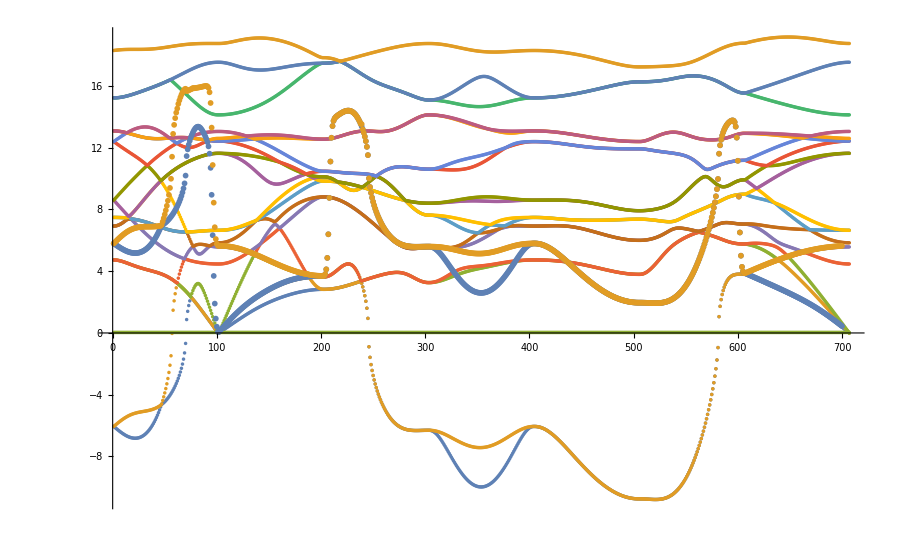

```mathematica
(*Set the value of the parameters for the interpolation*)
With[{mu=0.01*5,beta=100,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/T0,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*((Sqrt[Tfrac]*-Transpose[Join@@l1][[2]][[i]])-omega0R)},{i,1,700}];
transformedBandB=Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*((Sqrt[Tfrac]*-Transpose[Join@@l1][[2]][[i]])-omega0R)},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

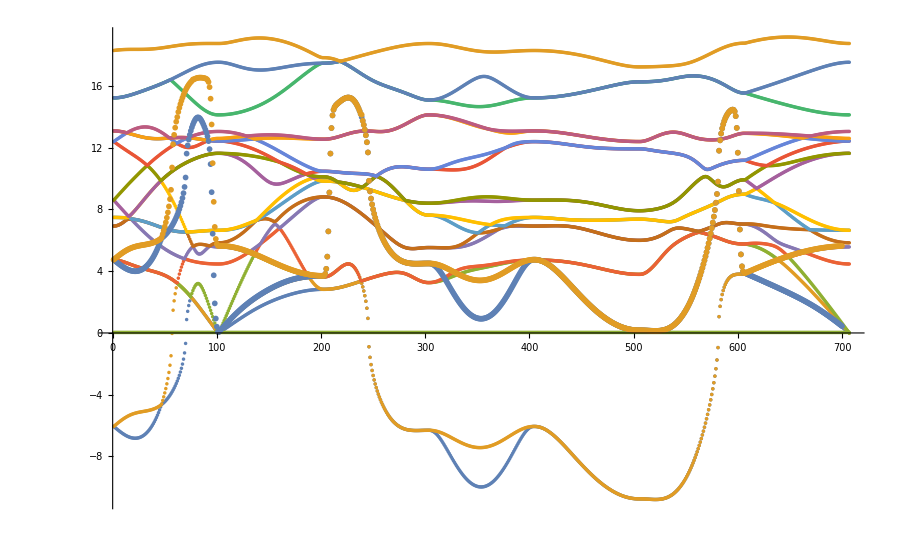

```mathematica
(*Set the value of the parameters for the interpolation*)
With[{mu=0.01*5,beta=100,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/Tc,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

## Force constant Hessian matrix

```mathematica
listFCvo2=ReadList["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b/FCnew",Number];
```

```mathematica
(*3natoms = 3*2*2*3*6=216*)
```

```mathematica
listFCvo2//Dimensions
listFCvo2Part=Partition[listFCvo2,216];
```

{46656}

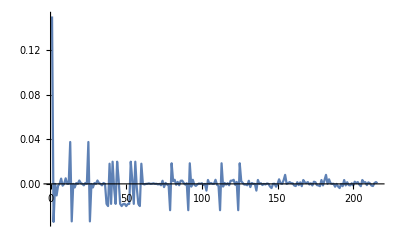

```mathematica
(*Row 1 of the Hessian*)
ListLinePlot[listFCvo2Part[[1]],PlotRange->All]
```

```mathematica
(*The sum rule is more or less satisfied - translational invariance*)
Table[Total@listFCvo2Part[[i]],{i,1,Length@listFCvo2Part}][[1;;10]]
```

{-4.15249×10^-8,-4.15249×10^-8,-4.85723×10^-17,-4.15249×10^-8,-4.15249×10^-8,-5.55112×10^-17,-4.15249×10^-8,-4.15249×10^-8,-4.85723×10^-17,-4.15249×10^-8}

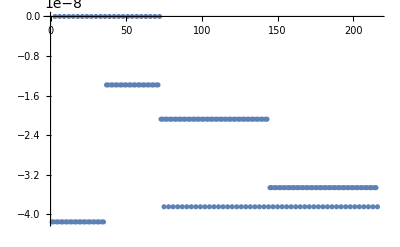

```mathematica
ListPlot@Table[Total@listFCvo2Part[[i]],{i,1,Length@listFCvo2Part}]
```

## Exact transformation at q_z=0 and q_z=0.5 + Gaussian interpolation for 0<q_z<0.5

#### Apply the transition only at q_z=0.5, setting it to zero for 0<q_z<0.5

```mathematica
(*Note, the bits set to zero are deleted to remove those data points*)
transformedBandA=Join[Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,95,100}],Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,295,302}],Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,507,511}],DeleteCases[Table[{Transpose[Join@@l1][[1]][[i]],tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*Transpose[Join@@l1][[2]][[i]]+tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*((Sqrt[Tfrac]*-Transpose[Join@@l1][[2]][[i]])-omega0R)},{i,2,700}],x_/;x[[2]]<0.00010]];
transformedBandB=Join[Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]},{i,295,302}],Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,507,511}],DeleteCases[Table[{Transpose[Join@@l2][[1]][[i]],tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*Transpose[Join@@l2][[2]][[i]]+tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*((Sqrt[Tfrac]*-Transpose[Join@@l1][[2]][[i]])-omega0R)},{i,1,700}],x_/;x[[2]]<0.000010]];
```

```mathematica
transformedBandA;
```

```mathematica
Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,90,100}]
```

{{90,2.24679},{91,2.05884},{92,1.86518},{93,1.66701},{94,1.46524},{95,1.26058},{96,1.05365},{97,0.844914},{98,0.634815},{99,0.423722},{100,0.211963}}

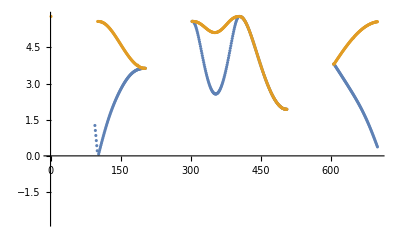

```mathematica
ListPlot@Join@{transformedBandA,transformedBandB}
```

#### Get data to train Gaussian process ML interpolation

Make the initial data set like {index,qz,qy,qz,transformationBandEnergy}

```mathematica
vo2Data[[90;;110]]//TableForm
```

90 | 0. | 0. | 0.055 | 1.04019 | 1.04019 | 2.24679 | 4.5038 | 5.43771 | 5.68859 | 6.6246 | 6.6246 | 11.5407 | 11.5407 | 12.4223 | 12.4949 | 12.4949 | 12.9964 | 14.3637 | 17.446 | 18.7564 | 0.0333687 | 0.11
91 | 0. | 0. | 0.05 | 0.947226 | 0.947226 | 2.05884 | 4.49769 | 5.50107 | 5.67329 | 6.62886 | 6.62886 | 11.5568 | 11.5568 | 12.4515 | 12.4859 | 12.4859 | 13.0068 | 14.3254 | 17.4619 | 18.7567 | 0.0333687 | 0.1
92 | 0. | 0. | 0.045 | 0.853798 | 0.853798 | 1.86518 | 4.4922 | 5.56121 | 5.65783 | 6.63281 | 6.63281 | 11.5717 | 11.5717 | 12.4773 | 12.4773 | 12.4788 | 13.0162 | 14.2901 | 17.4763 | 18.7568 | 0.0333687 | 0.09
93 | 0. | 0. | 0.04 | 0.759956 | 0.759956 | 1.66701 | 4.48732 | 5.61704 | 5.64267 | 6.63644 | 6.63644 | 11.5852 | 11.5852 | 12.4692 | 12.4692 | 12.504 | 13.0246 | 14.258 | 17.4894 | 18.7569 | 0.0333687 | 0.08
94 | 0. | 0. | 0.035 | 0.665748 | 0.665748 | 1.46524 | 4.48304 | 5.62826 | 5.66776 | 6.63969 | 6.63969 | 11.5973 | 11.5973 | 12.4619 | 12.4619 | 12.5268 | 13.032 | 14.2292 | 17.5009 | 18.7569 | 0.0333687 | 0.07
95 | 0. | 0. | 0.03 | 0.571221 | 0.571221 | 1.26058 | 4.47935 | 5.61497 | 5.71273 | 6.64257 | 6.64257 | 11.608 | 11.608 | 12.4553 | 12.4553 | 12.547 | 13.0385 | 14.204 | 17.511 | 18.7568 | 0.0333687 | 0.06
96 | 0. | 0. | 0.025 | 0.476421 | 0.476421 | 1.05365 | 4.47624 | 5.60315 | 5.75147 | 6.64503 | 6.64503 | 11.6172 | 11.6172 | 12.4495 | 12.4495 | 12.5644 | 13.0439 | 14.1824 | 17.5195 | 18.7568 | 0.0333687 | 0.05
97 | 0. | 0. | 0.02 | 0.381394 | 0.381394 | 0.844914 | 4.47371 | 5.59308 | 5.78363 | 6.64708 | 6.64708 | 11.6248 | 11.6248 | 12.4447 | 12.4447 | 12.5789 | 13.0484 | 14.1645 | 17.5265 | 18.7567 | 0.0333687 | 0.04
98 | 0. | 0. | 0.015 | 0.286183 | 0.286183 | 0.634815 | 4.47175 | 5.585 | 5.8089 | 6.64868 | 6.64868 | 11.6308 | 11.6308 | 12.4409 | 12.4409 | 12.5903 | 13.0518 | 14.1505 | 17.532 | 18.7566 | 0.0333687 | 0.03
99 | 0. | 0. | 0.01 | 0.190827 | 0.190827 | 0.423722 | 4.47035 | 5.57909 | 5.8271 | 6.64983 | 6.64983 | 11.6351 | 11.6351 | 12.4381 | 12.4381 | 12.5985 | 13.0543 | 14.1405 | 17.5359 | 18.7565 | 0.0333687 | 0.02
100 | 0. | 0. | 0.005 | 0.0953377 | 0.0953377 | 0.211963 | 4.46951 | 5.5755 | 5.83808 | 6.65053 | 6.65053 | 11.6377 | 11.6377 | 12.4364 | 12.4364 | 12.6034 | 13.0558 | 14.1344 | 17.5383 | 18.7565 | 0.0333687 | 0.01
101 | 0. | 0. | 0. | -0.00563432 | -0.004994 | -0.004994 | 4.46923 | 5.57429 | 5.84174 | 6.65076 | 6.65076 | 11.6386 | 11.6386 | 12.4359 | 12.4359 | 12.6051 | 13.0563 | 14.1324 | 17.5391 | 18.7565 | 0.0333687 | 0
102 | 0. | 0. | 0. | -0.00563432 | -0.004994 | -0.004994 | 4.46923 | 5.57429 | 5.84174 | 6.65076 | 6.65076 | 11.6386 | 11.6386 | 12.4359 | 12.4359 | 12.6051 | 13.0563 | 14.1324 | 17.5391 | 18.7565 | 0.0333687 | 0
103 | 0.005 | 0.005 | 0. | 0.0457738 | 0.0753184 | 0.160066 | 4.47035 | 5.57388 | 5.84297 | 6.65122 | 6.6514 | 11.6377 | 11.6384 | 12.4351 | 12.436 | 12.6056 | 13.0558 | 14.1328 | 17.538 | 18.7573 | 0.0333687 | 0
104 | 0.01 | 0.01 | 0. | 0.0919578 | 0.150863 | 0.320192 | 4.4737 | 5.57265 | 5.84667 | 6.65258 | 6.6533 | 11.635 | 11.6379 | 12.4327 | 12.4365 | 12.6073 | 13.0545 | 14.1341 | 17.5347 | 18.7598 | 0.0333687 | 0
105 | 0.015 | 0.015 | 0. | 0.138056 | 0.226157 | 0.480182 | 4.47927 | 5.57057 | 5.85286 | 6.65486 | 6.65647 | 11.6305 | 11.6371 | 12.4287 | 12.4373 | 12.6099 | 13.0523 | 14.1363 | 17.5293 | 18.7639 | 0.0333687 | 0
106 | 0.02 | 0.02 | 0. | 0.184137 | 0.301167 | 0.639997 | 4.48705 | 5.56761 | 5.86158 | 6.65805 | 6.6609 | 11.6242 | 11.6359 | 12.4234 | 12.4384 | 12.6134 | 13.0492 | 14.1393 | 17.5219 | 18.7695 | 0.0333687 | 0
107 | 0.025 | 0.025 | 0. | 0.230216 | 0.375816 | 0.799586 | 4.497 | 5.56371 | 5.87285 | 6.66217 | 6.66659 | 11.6162 | 11.6344 | 12.4168 | 12.4398 | 12.6177 | 13.0453 | 14.1432 | 17.5125 | 18.7766 | 0.0333687 | 0
108 | 0.03 | 0.03 | 0. | 0.276295 | 0.450025 | 0.958895 | 4.5091 | 5.55885 | 5.88671 | 6.66721 | 6.67351 | 11.6063 | 11.6326 | 12.4091 | 12.4415 | 12.6226 | 13.0404 | 14.148 | 17.5013 | 18.785 | 0.0333687 | 0
109 | 0.035 | 0.035 | 0. | 0.322374 | 0.523715 | 1.11787 | 4.5233 | 5.55297 | 5.90319 | 6.67319 | 6.68167 | 11.5946 | 11.6304 | 12.4003 | 12.4436 | 12.628 | 13.0347 | 14.1536 | 17.4884 | 18.7947 | 0.0333687 | 0
110 | 0.04 | 0.04 | 0. | 0.368448 | 0.596809 | 1.27645 | 4.53956 | 5.54606 | 5.92228 | 6.68012 | 6.69104 | 11.581 | 11.6279 | 12.3906 | 12.4459 | 12.6339 | 13.0281 | 14.1601 | 17.4741 | 18.8054 | 0.0333687 | 0

```mathematica
((Sqrt[Tfrac]*-Transpose[Join@@l1][[2]][[i]])-omega0R)
```

```mathematica
transformedBandAq3=Join[Table[{Transpose[Join@@l1][[1]][[i]],Transpose[vo2Data][[2]][[i]],Transpose[vo2Data][[3]][[i]],Transpose[vo2Data][[4]][[i]],Transpose[Join@@l1][[2]][[i]]},{i,95,100}],DeleteCases[Table[{Transpose[Join@@l1][[1]][[i]],Transpose[vo2Data][[2]][[i]],Transpose[vo2Data][[3]][[i]],Transpose[vo2Data][[4]][[i]],tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*Transpose[Join@@l1][[2]][[i]]+tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*((Sqrt[Tfrac]*-Transpose[Join@@l1][[2]][[i]])-omega0R)},{i,1,700}],x_/;x[[5]]<0.00001]];
transformedBandBq3=DeleteCases[Table[{Transpose[Join@@l2][[1]][[i]],Transpose[vo2Data][[2]][[i]],Transpose[vo2Data][[3]][[i]],Transpose[vo2Data][[4]][[i]],tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*Transpose[Join@@l2][[2]][[i]]+tFunctionPiece[Transpose[vo2Data][[4]][[i]]]*tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*((Sqrt[Tfrac]*-Transpose[Join@@l1][[2]][[i]])-omega0R)},{i,1,700}],x_/;x[[5]]<0.000001];
```

#### Make the training set

Map {qx,qy,qz}->{transformationBandEnergy} for all transformed bands in the following part of the BZ: 0<qx<0.5 AND 0<qy<0.5 AND (qz=0 OR qz=0.5)

```mathematica
mapDataA={Transpose@Transpose[transformedBandAq3][[2;;4]]->Transpose[transformedBandAq3][[5]]};
mapDataB={Transpose@Transpose[transformedBandBq3][[2;;4]]->Transpose[transformedBandBq3][[5]]};
```

#### Train model

```mathematica
modelA=Predict[mapDataA[[1]],Method->"GaussianProcess"]
modelB=Predict[mapDataB[[1]],Method->"GaussianProcess"]
```

PredictorFunction[…]

PredictorFunction[…]

#### Make plotable

```mathematica
qList=Transpose@{Transpose[vo2Data][[2]],Transpose[vo2Data][[3]],Transpose[vo2Data][[4]]};
newBandA=Table[{i,modelA[qList[[i]]]},{i,1,700}];
newBandB=Table[{i,modelB[qList[[i]]]},{i,1,700}];
```

```mathematica
newBandAsdp=Table[{i,modelA[qList[[i]]]+StandardDeviation[modelA[qList[[i]],"Distribution"]]},{i,1,700}];
newBandBsdp=Table[{i,modelB[qList[[i]]]+StandardDeviation[modelB[qList[[i]],"Distribution"]]},{i,1,700}];
```

```mathematica
newBandAsdm=Table[{i,modelA[qList[[i]]]-StandardDeviation[modelA[qList[[i]],"Distribution"]]},{i,1,700}];
newBandBsdm=Table[{i,modelB[qList[[i]]]-StandardDeviation[modelB[qList[[i]],"Distribution"]]},{i,1,700}];
```

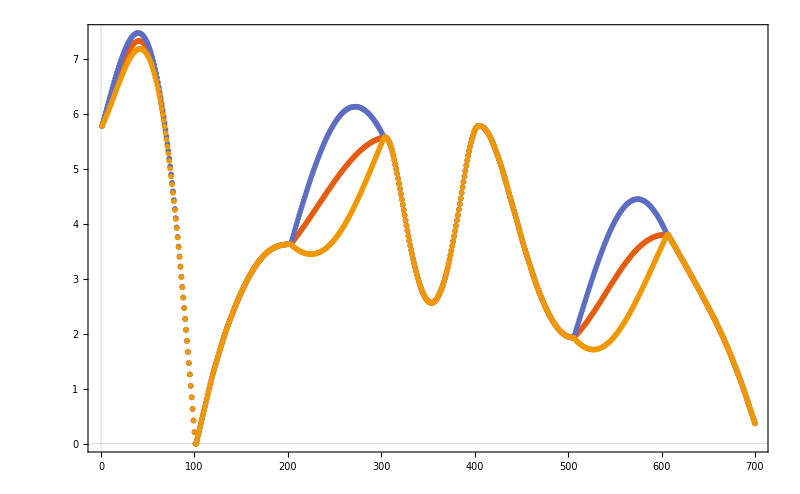

```mathematica
ListPlot[Join@{newBandA,newBandAsdp,newBandAsdm},PlotRange->All,PlotStyle->Directive[PointSize[0.005],18],PlotTheme->"Scientific",ImageSize->800]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,y,0}).

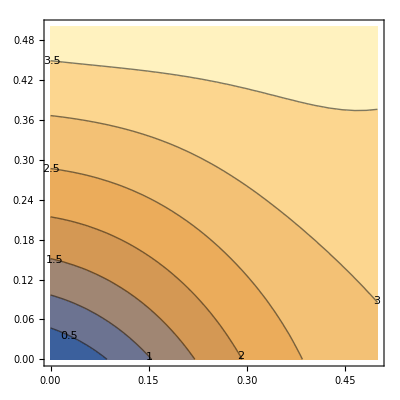

```mathematica
ContourPlot[Evaluate@modelA[{x,y,0}],{x,0,0.5},{y,0,0.5},ContourLabels->True]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({0,y,z}).

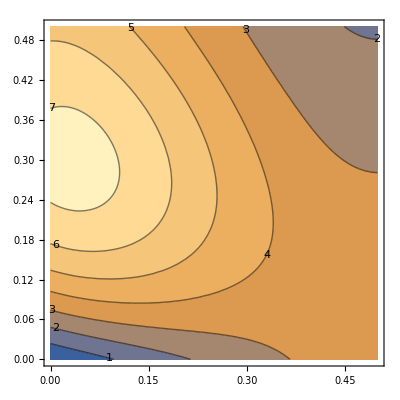

```mathematica
ContourPlot[Evaluate@modelA[{0,y,z}],{y,0,0.5},{z,0,0.5},ContourLabels->True]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({x,0,z}).

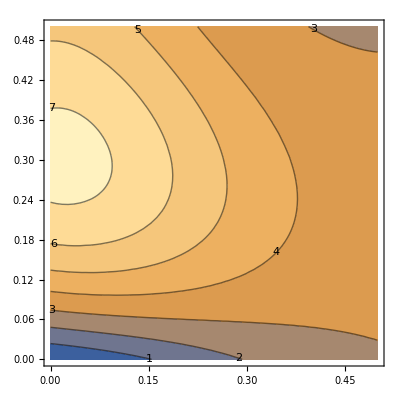

```mathematica
ContourPlot[Evaluate@modelA[{x,0,z}],{x,0,0.5},{z,0,0.5},ContourLabels->True]
```

```mathematica
Plot3D[Evaluate@modelA[{0,y,z}],{y,0,0.5},{z,0,0.5}]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value ({0,y,z}).

-Graphics3D-

```mathematica
newBandA=Table[{i,modelA[qList[[i]]]},{i,1,700}];
newBandB=Table[{i,modelB[qList[[i]]]},{i,1,700}];
```

#### Plot transformed bands with GP interpolation for 0<q_z<0.5

```mathematica
styleLegend[arg_]:=Style[ToString@arg,18]
```

```mathematica
labels={Style["i=1: {q_x,q_y,0<q_z<0.5} Gaussian interpolation",20,FontFamily->Times],Style["i=1: {q_x,q_y,q_z=0} and {q_x,q_y,q_z=0.5} transform",20,FontFamily->Times],Style["i=2: {q_x,q_y,0<q_z<0.5} Gaussian interpolation",20,FontFamily->Times],Style["i=2: {q_x,q_y,q_z=0} and {q_x,q_y,q_z=0.5} transform",20,FontFamily->Times]}
```

{i=1: {q_x,q_y,0<q_z<0.5} Gaussian interpolation,i=1: {q_x,q_y,q_z=0} and {q_x,q_y,q_z=0.5} transform,i=2: {q_x,q_y,0<q_z<0.5} Gaussian interpolation,i=2: {q_x,q_y,q_z=0} and {q_x,q_y,q_z=0.5} transform}

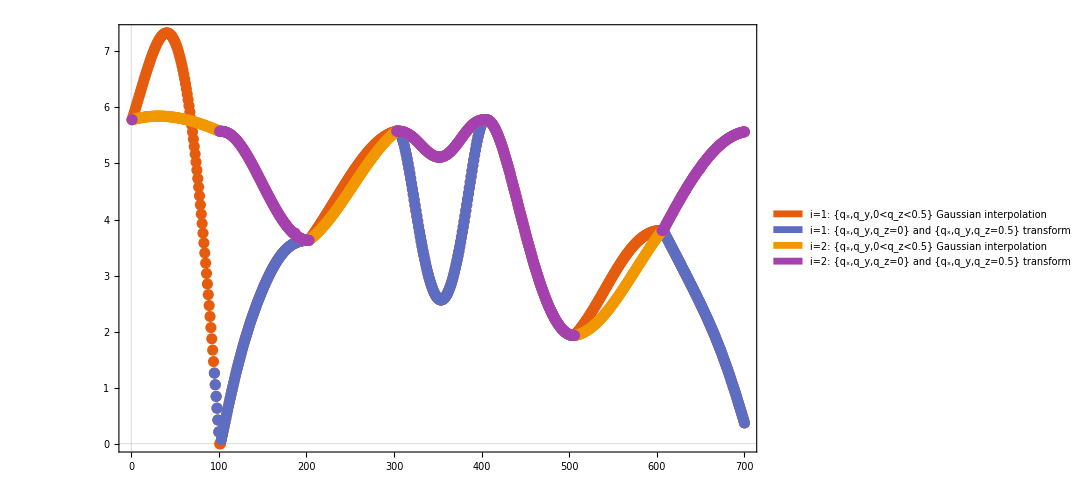

```mathematica
p1=ListPlot[Join@{newBandA,transformedBandA,newBandB,
transformedBandB},PlotRange->All,PlotStyle->Directive[PointSize[0.01],18],
PlotLegends->SwatchLegend@{labels},PlotTheme->"Scientific",ImageSize->800]
```

{50,0.,0.,0.255,-4.45239,-3.88347,3.72994,3.72994,5.44664,6.76361,6.76361,9.47111,10.0865,10.0865,11.7877,12.6071,12.6071,12.8565,16.2406,16.2406,18.4975,0.0333687,0.51}

{150,0.24,0.24,0.,1.98581,2.75016,4.62765,6.21104,6.62237,7.36422,7.79203,8.10285,9.78264,11.2546,11.4446,12.1377,12.6221,12.837,15.0751,17.068,19.0763,0.0333687,0}

{250,0.5,0.5,0.235,-2.75577,-2.75577,3.60621,3.60621,7.10434,7.10434,9.21833,9.21833,10.0008,10.0008,10.2209,10.2209,13.0672,13.0672,16.3457,16.3457,18.1711,0.0333687,0.47}

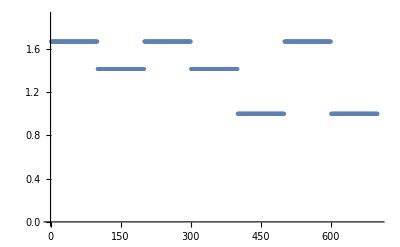

```mathematica
vo2Data[[50]]
vo2Data[[150]]
vo2Data[[250]]
cOVERa=1.668;
scaleFactors=Join[Table[cOVERa,{i,100}],Table[Sqrt[2],{i,100}],Table[cOVERa,{i,100}],Table[Sqrt[2],{i,100}],Table[1,{i,100}],Table[cOVERa,{i,100}],Table[1,{i,100}]];
ListPlot[scaleFactors,PlotRange->{Automatic,{0,1.9}}]
```

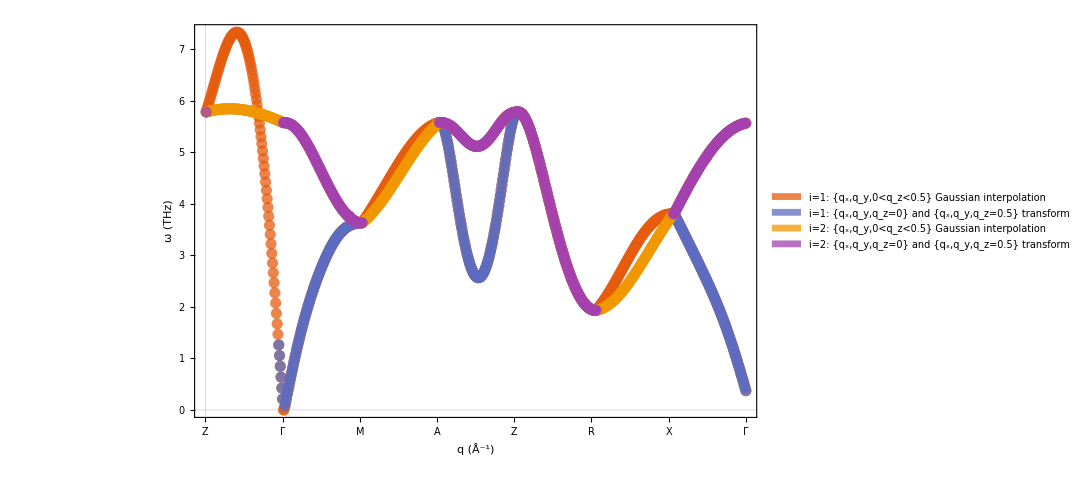

```mathematica
p1a=ListPlot[Join@{newBandA,transformedBandA,newBandB,
transformedBandB},PlotRange->All,FrameStyle->Directive[Black,18],FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotTheme->"Scientific",FrameTicks->{{Automatic,None},{{{0,Style["Z",20]},{100,Style["Γ",20]},{200,Style["M",20]},{300,Style["A",20]},{400,Style["Z",20]},{500,Style["R",20]},{600,Style["X",20]},{700,Style["Γ",20]}},None}},PlotStyle->Directive[PointSize[0.01],18,Opacity[0.75]],
PlotLegends->SwatchLegend@{labels},PlotTheme->"Scientific",ImageSize->800]
```

```mathematica
p1a=ListPlot[Join@{newBandA,transformedBandA,newBandB,
transformedBandB},PlotRange->All,FrameStyle->Directive[Black,18],FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotTheme->"Scientific",FrameTicks->{{Automatic,None},{{{0,Style["Z",20]},{100,Style["Γ",20]},{200,Style["M",20]},{300,Style["A",20]},{400,Style["Z",20]},{500,Style["R",20]},{600,Style["X",20]},{700,Style["Γ",20]}},None}},PlotStyle->Directive[PointSize[0.01],18,Opacity[0.75]],
PlotLegends->SwatchLegend@{labels},PlotTheme->"Scientific",ImageSize->800]
```

-Graphics-

```mathematica
labels2={Style["T=T_C \n Note: {q_x,q_y,q_z=0} fixed\n {q_x,q_y,q_z=0.5} transformed\n {q_x,q_y,0<q_z<0.5} interpolated",20,FontFamily->Times]}
```

{T=T_C 
 Note: {q_x,q_y,q_z=0} fixed
 {q_x,q_y,q_z=0.5} transformed
 {q_x,q_y,0<q_z<0.5} interpolated}

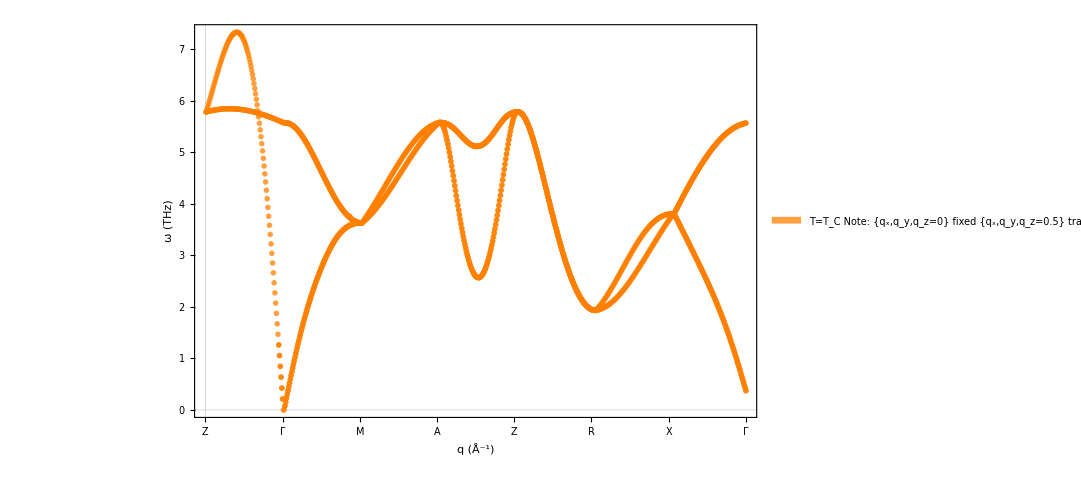

```mathematica
p1b=ListPlot[Join@{newBandA,transformedBandA,newBandB,
transformedBandB},PlotRange->All,FrameStyle->Directive[Black,18],FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotTheme->"Scientific",FrameTicks->{{Automatic,None},{{{0,Style["Z",20]},{100,Style["Γ",20]},{200,Style["M",20]},{300,Style["A",20]},{400,Style["Z",20]},{500,Style["R",20]},{600,Style["X",20]},{700,Style["Γ",20]}},None}},PlotStyle->Directive[Orange,PointSize[0.005],18,Opacity[0.75]],
PlotLegends->SwatchLegend@{labels2},PlotTheme->"Scientific",ImageSize->800]
```

```mathematica
p2=ListLinePlot[Table[originalBandi[i],{i,1,18}],AspectRatio->Sqrt[1/2],FrameStyle->Directive[Black,18],PlotStyle->Directive[Black,18],Frame->True,FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotTheme->"Scientific"];
```

```mathematica
p2a=ListLinePlot[Table[originalBandi[i],{i,1,18}],AspectRatio->Sqrt[1/2],FrameStyle->Directive[Black,18],PlotStyle->Directive[Dashing[0.012],Black,18],Frame->True,FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotTheme->"Scientific"];
```

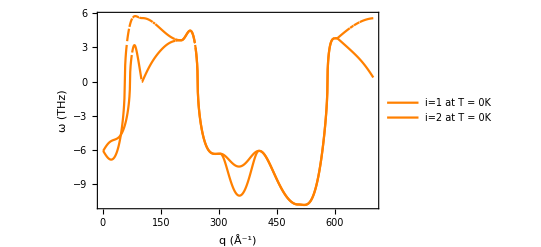

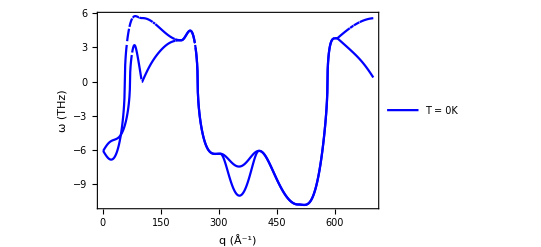

```mathematica
p3=ListLinePlot[Join@@{l1},PlotStyle->Directive[Dashed,Black],Frame->True,FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]}];
p3=ListLinePlot[Join@@{l1,l2},PlotStyle->Directive[Orange],Frame->True,FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotLegends->{Style["i=1 at T = 0K",18,FontFamily->Times],Style["i=2 at T = 0K",18,FontFamily->Times]}]

p3a=ListLinePlot[Join@@{l1,l2},PlotStyle->Directive[Blue],Frame->True,FrameLabel->{Style["q (Å^-1)",18],Style["ω (THz)",18]},PlotLegends->{Style["T = 0K",18,FontFamily->Times]}]
```

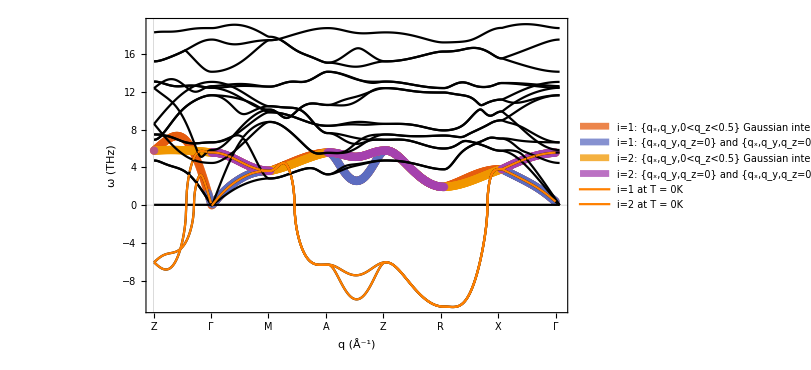

```mathematica
Show[{p1a,p2,p3},ImageSize->600,PlotRange->All]
```

```mathematica
Show[{p1a,p2,p3},ImageSize->600,PlotRange->All]
```

-Graphics-

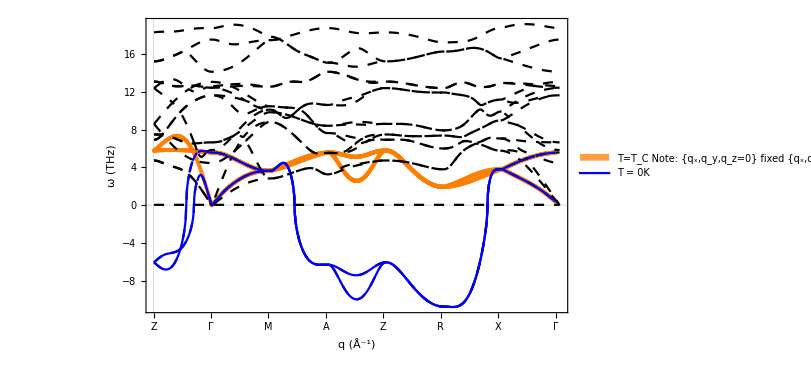

```mathematica
Show[{p1b,p2a,p3a},ImageSize->600,PlotRange->All]
```

```mathematica
(*NN-weighted interpolation*)
```

```mathematica
modelA["Parameters"]
```

PredictorFunction::mlincfttp: Incompatible variable type (NumericalVector) and variable value (Parameters).

PredictorFunction[…][Parameters]

```mathematica
PredictorInformation[modelA]
```

Predictor information
Method | Gaussian Process
Number of features | 1
Number of training examples | 407
AssumeDeterministic | False
Numerical Covariance Type | SquaredExponential
Nominal Covariance Type | HammingDistance
EstimationMethod | MaximumPosterior
OptimizationMethod | FindMinimum

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b/"]
list=ReadList["mesh.out",Table[Number,{i,21}]];
fx[band_]:={#[[2]],#[[3]],#[[band+3]]}&/@list;
fy[band_]:={#[[1]],#[[3]],#[[band+3]]}&/@list;
fz[band_]:={#[[1]],#[[2]],#[[band+3]]}&/@list;
listd=ReadList["dense_mesh.out",Table[Number,{i,21}]];
fdx[band_]:={#[[2]],#[[3]],#[[band+3]]}&/@listd;
fdy[band_]:={#[[1]],#[[3]],#[[band+3]]}&/@listd;
fdz[band_]:={#[[1]],#[[2]],#[[band+3]]}&/@listd;listdv=ReadList["vdense_mesh.out",Table[Number,{i,21}]];
fvdx[band_]:={#[[2]],#[[3]],#[[band+3]]}&/@listdv;
fvdy[band_]:={#[[1]],#[[3]],#[[band+3]]}&/@listdv;
fvdz[band_]:={#[[1]],#[[2]],#[[band+3]]}&/@listdv;
```

/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b

```mathematica
denseList={#[[1]],#[[2]],#[[3]],#[[1+3]]}&/@listd;
```

```mathematica
denseList[[1]]
```

{0.03125,0.03125,0.03125,0.65747}

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b/"]
listd=ReadList["dense_mesh.out",Table[Number,{i,21}]];
denseList1={#[[1]],#[[2]],#[[3]],#[[1+3]]}&/@listd;
qGE3denseList1=DeleteCases[Table[If[denseList1[[i]][[3]]>0.1,denseList1[[i]],0],{i,1,Length@denseList1}],0];
denseList2={#[[1]],#[[2]],#[[3]],#[[2+3]]}&/@listd;
qGE3denseList2=DeleteCases[Table[If[denseList2[[i]][[3]]>0.1,denseList2[[i]],0],{i,1,Length@denseList2}],0];
```

/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b

```mathematica
qGE3denseList1[[1]]
```

{0.03125,0.03125,0.21875,-3.95648}

```mathematica
ListPlot3D@{Transpose@{Transpose[qGE3denseList1][[1]],Transpose[qGE3denseList1][[3]],Transpose[qGE3denseList1][[4]]},Transpose@{Transpose[qGE3denseList2][[1]],Transpose[qGE3denseList2][[3]],Transpose[qGE3denseList2][[4]]}}
ListPlot3D@{Transpose@{Transpose[qGE3denseList1][[2]],Transpose[qGE3denseList1][[3]],Transpose[qGE3denseList1][[4]]},Transpose@{Transpose[qGE3denseList2][[2]],Transpose[qGE3denseList2][[3]],Transpose[qGE3denseList2][[4]]}}
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPlot3D@{Transpose@{Transpose[qGE3denseList1][[2]],Transpose[qGE3denseList1][[3]],Transpose[qGE3denseList1][[4]]},Transpose@{Transpose[qGE3denseList2][[2]],Transpose[qGE3denseList2][[3]],Transpose[qGE3denseList2][[4]]}}
```

-Graphics3D-

```mathematica
qGE3denseList1b1=DeleteCases[Table[If[denseList1[[i]][[3]]>0.3,denseList1[[i]],0],{i,1,Length@denseList1}],0];
qGE3denseList2b2=DeleteCases[Table[If[denseList2[[i]][[3]]>0.3,denseList2[[i]],0],{i,1,Length@denseList2}],0];
```

```mathematica
qGE3denseList1b1
```

{{0.03125,0.03125,0.34375,-6.62246},{0.09375,0.03125,0.34375,-7.09454},{0.15625,0.03125,0.34375,-7.83579},{0.21875,0.03125,0.34375,-8.63739},{0.28125,0.03125,0.34375,-9.36377},{0.34375,0.03125,0.34375,-9.93584},{0.40625,0.03125,0.34375,-10.3076},{0.46875,0.03125,0.34375,-10.4528},{0.09375,0.09375,0.34375,-7.64737},{0.15625,0.09375,0.34375,-8.37383},{0.21875,0.09375,0.34375,-9.07527},{0.28125,0.09375,0.34375,-9.65866},{0.34375,0.09375,0.34375,-10.0723},{0.40625,0.09375,0.34375,-10.2855},{0.46875,0.09375,0.34375,-10.2812},{0.15625,0.15625,0.34375,-8.96365},{0.21875,0.15625,0.34375,-9.47023},{0.28125,0.15625,0.34375,-9.83976},{0.34375,0.15625,0.34375,-10.042},{0.40625,0.15625,0.34375,-10.0594},{0.46875,0.15625,0.34375,-9.88474},{0.21875,0.21875,0.34375,-9.74206},{0.28125,0.21875,0.34375,-9.86559},{0.34375,0.21875,0.34375,-9.82997},{0.40625,0.21875,0.34375,-9.63325},{0.46875,0.21875,0.34375,-9.28248},{0.28125,0.28125,0.34375,-9.73294},{0.34375,0.28125,0.34375,-9.44987},{0.40625,0.28125,0.34375,-9.03373},{0.46875,0.28125,0.34375,-8.51386},{0.34375,0.34375,0.34375,-8.92799},{0.40625,0.34375,0.34375,-8.30534},{0.46875,0.34375,0.34375,-7.64528},{0.40625,0.40625,0.34375,-7.51903},{0.46875,0.40625,0.34375,-6.79018},{0.46875,0.46875,0.34375,-6.13887},{0.03125,0.03125,0.40625,-6.93577},{0.09375,0.03125,0.40625,-7.39199},{0.15625,0.03125,0.40625,-8.12214},{0.21875,0.03125,0.40625,-8.92419},{0.28125,0.03125,0.40625,-9.65823},{0.34375,0.03125,0.40625,-10.2398},{0.40625,0.03125,0.40625,-10.6188},{0.46875,0.03125,0.40625,-10.7666},{0.09375,0.09375,0.40625,-7.90775},{0.15625,0.09375,0.40625,-8.62045},{0.21875,0.09375,0.40625,-9.32682},{0.28125,0.09375,0.40625,-9.92392},{0.34375,0.09375,0.40625,-10.3538},{0.40625,0.09375,0.40625,-10.582},{0.46875,0.09375,0.40625,-10.5891},{0.15625,0.15625,0.40625,-9.19912},{0.21875,0.15625,0.40625,-9.71057},{0.28125,0.15625,0.40625,-10.0931},{0.34375,0.15625,0.40625,-10.3119},{0.40625,0.15625,0.40625,-10.3465},{0.46875,0.15625,0.40625,-10.1878},{0.21875,0.21875,0.40625,-9.9836},{0.28125,0.21875,0.40625,-10.1159},{0.34375,0.21875,0.40625,-10.0939},{0.40625,0.21875,0.40625,-9.9139},{0.46875,0.21875,0.40625,-9.58235},{0.28125,0.28125,0.40625,-9.98677},{0.34375,0.28125,0.40625,-9.71301},{0.40625,0.28125,0.40625,-9.31212},{0.46875,0.28125,0.40625,-8.81464},{0.34375,0.34375,0.40625,-9.19678},{0.40625,0.34375,0.40625,-8.58871},{0.46875,0.34375,0.40625,-7.95596},{0.40625,0.40625,0.40625,-7.81969},{0.46875,0.40625,0.40625,-7.12574},{0.46875,0.46875,0.40625,-6.51213},{0.03125,0.03125,0.46875,-6.54138},{0.09375,0.03125,0.46875,-7.07168},{0.15625,0.03125,0.46875,-7.88461},{0.21875,0.03125,0.46875,-8.75163},{0.28125,0.03125,0.46875,-9.53449},{0.34375,0.03125,0.46875,-10.1542},{0.40625,0.03125,0.46875,-10.5645},{0.46875,0.03125,0.46875,-10.7388},{0.09375,0.09375,0.46875,-7.69801},{0.15625,0.09375,0.46875,-8.46915},{0.21875,0.09375,0.46875,-9.21079},{0.28125,0.09375,0.46875,-9.8348},{0.34375,0.09375,0.46875,-10.2881},{0.40625,0.09375,0.46875,-10.5376},{0.46875,0.09375,0.46875,-10.5643},{0.15625,0.15625,0.46875,-9.07755},{0.21875,0.15625,0.46875,-9.60762},{0.28125,0.15625,0.46875,-10.0078},{0.34375,0.15625,0.46875,-10.2454},{0.40625,0.15625,0.46875,-10.3},{0.46875,0.15625,0.46875,-10.1622},{0.21875,0.21875,0.46875,-9.88942},{0.28125,0.21875,0.46875,-10.033},{0.34375,0.21875,0.46875,-10.0261},{0.40625,0.21875,0.46875,-9.86508},{0.46875,0.21875,0.46875,-9.5561},{0.28125,0.28125,0.46875,-9.90998},{0.34375,0.28125,0.46875,-9.6474},{0.40625,0.28125,0.46875,-9.26353},{0.46875,0.28125,0.46875,-8.7898},{0.34375,0.34375,0.46875,-9.13855},{0.40625,0.34375,0.46875,-8.5451},{0.46875,0.34375,0.46875,-7.93683},{0.40625,0.40625,0.46875,-7.78909},{0.46875,0.40625,0.46875,-7.11976},{0.46875,0.46875,0.46875,-6.52625}}

```mathematica
data=Flatten[Table[{x,y,x^2+y^2},{x,-10,10},{y,-10,10}],1];
```

```mathematica
f[1][[1;;5]]
```

{{0.0625,0.0625,0.0625,1.2847},{0.1875,0.0625,0.0625,2.07462},{0.3125,0.0625,0.0625,2.76936},{0.4375,0.0625,0.0625,3.37227},{0.1875,0.1875,0.0625,1.88443}}

```mathematica
f[band_]:=({#[[1]],#[[2]],#[[3]]}&/@list)->(#[[band+3]]&/@list)
fdv[band_]:=({#[[1]],#[[2]],#[[3]]}&/@listdv)->(#[[band+3]]&/@listdv)
```

```mathematica
qValsDV=Transpose[listdv][[1]][[1;;16]]
qVals={0.00625,0.1875,0.3125,0.4375};
```

{0.015625,0.046875,0.078125,0.109375,0.140625,0.171875,0.203125,0.234375,0.265625,0.296875,0.328125,0.359375,0.390625,0.421875,0.453125,0.484375}

```mathematica
f[2][[2]]
```

{1.81938,2.69948,3.86191,3.92313,2.84288,3.44945,3.82931,3.54949,3.63158,3.26133,2.57623,-2.08439,-4.32741,-5.54687,0.793995,-2.90663,-4.44633,1.03578,-2.20354,2.62383,-5.43531,-6.7733,-8.51118,-9.67935,-6.31692,-7.2281,-8.51458,-6.3217,-6.79841,-5.59102,-5.97374,-7.40701,-9.19507,-10.3977,-7.16974,-8.05725,-9.2624,-7.27268,-7.6184,-6.50285}

```mathematica
fdv[1];
```

```mathematica
f1=Table[Predict[f[i],Method->"GaussianProcess"],{i,1,8}]
f1dv=Table[Predict[fdv[i],Method->"GaussianProcess"],{i,1,8}]
```

{PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…]}

{PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…],PredictorFunction[…]}

```mathematica
ListPlot3D[Table[f1[[1]][{x,0,z}],{x,0,1,0.1},{z,0,1,0.1}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[f1[[2]][{x,0,z}],{x,0,1,0.1},{z,0,1,0.1}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[f1[[3]][{x,0,z}],{x,0,1,0.1},{z,0,1,0.1}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[f1[[4]][{x,0,z}],{x,0,1,0.1},{z,0,1,0.1}],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[f1[[5]][{x,0,z}],{x,0,1,0.1},{z,0,1,0.1}],PlotRange->All]
```

-Graphics3D-

```mathematica
f1[[1]][{qVals[[1]],qVals[[1]],qVals[[1]]}]
```

1.28256

```mathematica
ListPlot3D@Flatten[Table[{qVals[[i]],qVals[[j]],f1[[3]][{qVals[[i]],qVals[[1]],qVals[[j]]}]},{i,1,4},{j,1,4}],1]
```

-Graphics3D-

```mathematica
ListPlot3D@Flatten[Table[{qVals[[i]],qVals[[j]],f1[[2]][{qVals[[i]],qVals[[1]],qVals[[j]]}]},{i,1,4},{j,1,4}],1]
```

-Graphics3D-

```mathematica
ListPlot3D@Flatten[Table[{qVals[[i]],qVals[[j]],f1[[1]][{qVals[[i]],qVals[[1]],qVals[[j]]}]},{i,1,4},{j,1,4}],1]
```

-Graphics3D-

```mathematica
qVals
```

{0.00625,0.1875,0.3125,0.4375}

```mathematica
ListLinePlot@Table[Table[{qValsDV[[i]],f1dv[[j]][{qValsDV[[i]],qValsDV[[1]],qValsDV[[1]]}]},{i,1,16}],{j,1,8}]
```

```mathematica
qValsDV[[1]]
qVals[[1]]
```

0.015625

0.00625

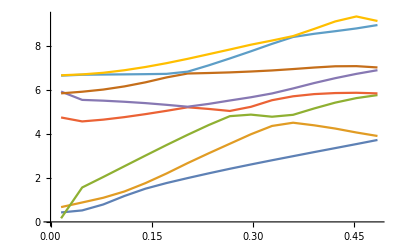

```mathematica
p1=ListLinePlot@Table[Table[{qValsDV[[i]],f1dv[[j]][{qValsDV[[i]],qValsDV[[2]],qValsDV[[1]]}]},{i,1,16}],{j,1,8}]
```

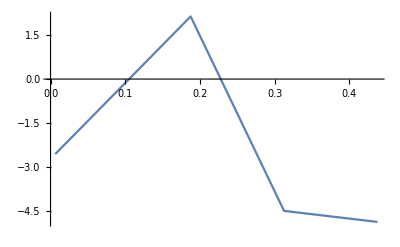

```mathematica
ListLinePlot@Table[{qVals[[i]],f1[[2]][{qVals[[1]],qVals[[1]],qVals[[i]]}]},{i,1,4}]
```

```mathematica
f1[[2]][{qVals[[1]],qVals[[1]],qVals[[1]]}]
```

-2.56196

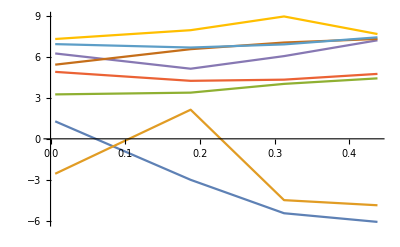

```mathematica
ListLinePlot@Table[Table[{qVals[[i]],f1[[j]][{qVals[[1]],qVals[[1]],qVals[[i]]}]},{i,1,4}],{j,1,8}]
```

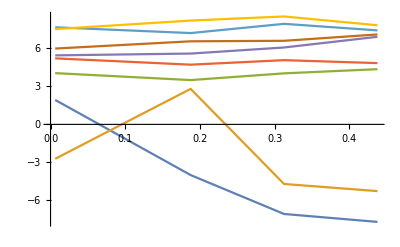
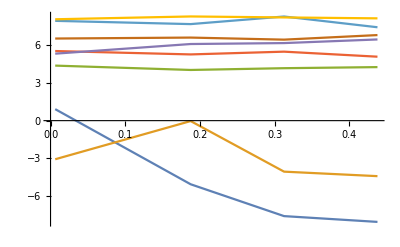
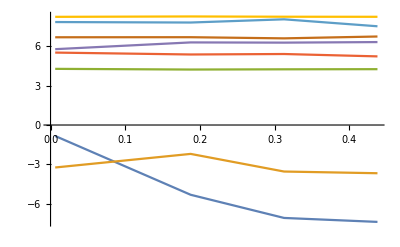
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListLinePlot@Table[Table[{qVals[[i]],f1[[j]][{qVals[[1]],qVals[[k]],qVals[[i]]}]},{i,1,4}],{j,1,8}],{k,1,4}]
```

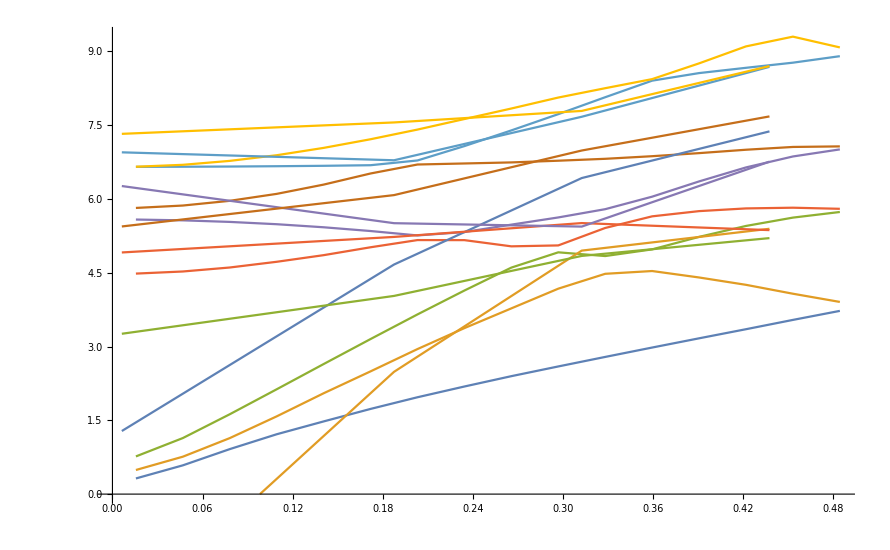

```mathematica
Show[p1,p2]
```

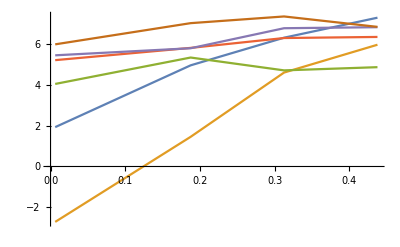

```mathematica
ListLinePlot@Table[Table[{qVals[[i]],f1[[j]][{qVals[[i]],qVals[[2]],qVals[[1]]}]},{i,1,4}],{j,1,6}]
```

```mathematica
ListPlot3D[Table[fy[i],{i,1,5}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1]]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fvdx[i],{i,1,5}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1]]
```

-Graphics3D-

```mathematica
fy[1]
```

{{0.0625,0.0625,1.2847},{0.1875,0.0625,2.07462},{0.3125,0.0625,2.76936},{0.4375,0.0625,3.37227},{0.1875,0.0625,1.88443},{0.3125,0.0625,2.64565},{0.4375,0.0625,3.36189},{0.3125,0.0625,2.47653},{0.4375,0.0625,3.09499},{0.4375,0.0625,2.85756},{0.0625,0.1875,-3.46639},{0.1875,0.1875,-4.70577},{0.3125,0.1875,-5.65993},{0.4375,0.1875,-5.97848},{0.1875,0.1875,-5.30176},{0.3125,0.1875,-5.56474},{0.4375,0.1875,-5.29908},{0.3125,0.1875,-4.94692},{0.4375,0.1875,-3.8354},{0.4375,0.1875,-1.14355},{0.0625,0.3125,-6.5392},{0.1875,0.3125,-8.07257},{0.3125,0.3125,-9.39474},{0.4375,0.3125,-9.98365},{0.1875,0.3125,-9.07185},{0.3125,0.3125,-9.5546},{0.4375,0.3125,-9.36746},{0.3125,0.3125,-9.04187},{0.4375,0.3125,-7.99893},{0.4375,0.3125,-6.33177},{0.0625,0.4375,-7.20002},{0.1875,0.4375,-8.67581},{0.3125,0.4375,-10.0506},{0.4375,0.4375,-10.6918},{0.1875,0.4375,-9.63967},{0.3125,0.4375,-10.1691},{0.4375,0.4375,-10.048},{0.3125,0.4375,-9.66251},{0.4375,0.4375,-8.67632},{0.4375,0.4375,-7.09769}}

```mathematica
Show[ListPlot3D[Table[fvdy[i],{i,1,5}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1]]
```

-Graphics3D-

```mathematica
(*Procedure to identify what {qx,qy,qz} values are transition bands in the irred BZ mesh - 
Plot bands along high symmetry directions
Identify the low two transition bands by hand
Interpolate using GP
Apply the GP to points in the generalised irreducible BZ mesh
*)
```